```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.25; (* induced gap in meV *)
Nx=500;
Nxn=120;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=0.4;
```

```mathematica
Mag={};
For[l=2,l≤502,l++,
out=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Magnetic Profile\\Matlab_output.txt",{"Lines",l}];
otp="{"<>out<>"}";
otp=StringReplace[otp,{"e" :> "*10^"}];
mtp=ToExpression[otp];
Mag=Join[Mag,{mtp}];
];
```

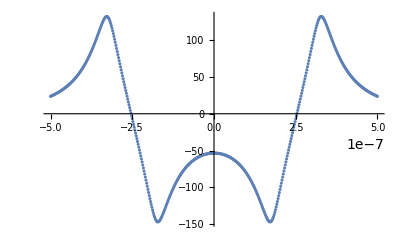

```mathematica
ListPlot[Mag]
```

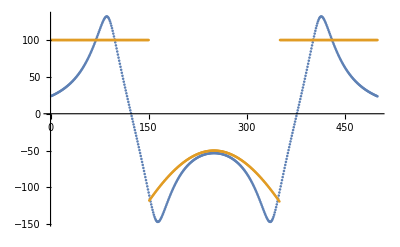

```mathematica
MagΔ=Table[Mag[[Ceiling[ii*Length[Mag]/Nx],2]],{ii,1,Nx}];
MagΔ0=100-300*Table[(HeavisideTheta[ii-150.1]-HeavisideTheta[ii-350.1])*(1-0.5Cos[(ii-250)/100]),{ii,1,Nx}];
ListPlot[{MagΔ,MagΔ0}]
```

```mathematica
Clear[Hs, Es, Hs0];
Hs[μ_, δμ_, Γ_]:=Block[{etp, ii, jj, nn, ϵ0},
νμ=1;                            (* !!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!! *) 
etp=Table[0,{s,1,2Nx*Ny},{s,1,2Nx*Ny}];
For[jj=1,jj≤Ny,jj++,
For[ii=1,ii≤Nx,ii++,
nn=(jj-1)*2Nx+2ii-1;
ϵ0=2ts Cos[Pi/(Nx+1.0)]+2tsw Cos[νμ*Pi/(Ny+1.0)];
etp[[nn,nn]]=-μ +ϵ0 ;
etp[[nn+1,nn+1]]=etp[[nn,nn]];
etp[[nn,nn+1]]=Γ*MagΔ[[ii]];
etp[[nn+1,nn]]=Γ*MagΔ[[ii]];
];
];
For[jj=1,jj≤Ny,jj++,
For[ii=1,ii≤Nx-1,ii++,
nn=(jj-1)*2Nx+2ii-1;
etp[[nn, nn+2]]=-ts;          etp[[nn+2, nn]]=-ts;
etp[[nn+1, nn+3]]=-ts;   etp[[nn+3, nn+1]]=-ts;
];
];
For[ii=1,ii≤Nx,ii++,
For[jj=1,jj≤Ny-1,jj++,
nn=(jj-1)*2Nx+2ii-1;
etp[[nn, nn+2Nx]]=-tsw;                  etp[[nn+2Nx, nn]]=-tsw;
etp[[nn+1, nn+2Nx+1]]=-tsw;    etp[[nn+2Nx+1, nn+1]]=-tsw;
];
];
For[jj=1,jj≤Ny,jj++,
For[ii=1,ii≤Nx-1,ii++,
nn=(jj-1)*2Nx+2ii-1;
etp[[nn, nn+3]] = α/2;              etp[[nn+3, nn]] = α/2;
etp[[nn+1, nn+2]] = -α/2;     etp[[nn+2, nn+1]] = -α/2;
];
];
For[ii=1,ii≤Nx,ii++,
For[jj=1,jj≤Ny-1,jj++,
nn=(jj-1)*2Nx+2ii-1;
etp[[nn, nn+2Nx+1]]=-ⅈ*αw/2;        etp[[nn+2Nx+1, nn]]=ⅈ*αw/2;
etp[[nn+1, nn+2Nx]]=-ⅈ*αw/2;        etp[[nn+2Nx, nn+1]]=ⅈ*αw/2;
];
];
etp
];
Es:=Sort[Eigenvalues[Hs0]];
```

```mathematica
Clear[Hd];
Hd=Block[{etp, ii, jj, nn, ϵ0},
etp=Table[0,{s,1,2Nx*Ny},{s,1,2Nx*Ny}];
For[jj=1,jj≤Ny,jj++,
For[ii=1,ii≤Nx,ii++,
nn=(jj-1)*2Nx+2ii-1;
etp[[nn,nn]]=ⅈ ;
etp[[nn+1,nn+1]]=etp[[nn,nn]];
];
];
etp
];
Es:=Sort[Eigenvalues[Hs0]];
```

```mathematica
Clear[HsBdG, HΔ, EsBdG];
HΔ=Block[{etp},
etp=Table[0,{s,1,2Nx*Ny},{s,1,2Nx*Ny}];
For[jj=1,jj≤Ny,jj++,
For[ii=Nxn+1,ii≤Nx-Nxn,ii++,
nn=(jj-1)*2Nx+2ii-1;
etp[[nn,nn+1]]=Δ;
etp[[nn+1,nn]]=-Δ;
];
];
etp
];
```

```mathematica
Clear[HsBdG,HΔBdG];
HBdG[μ_, δμ_, Γ_]:=ArrayFlatten[{{Hs[μ, δμ, Γ], HΔ},{-HΔ, -Transpose[Hs[μ, δμ, Γ]]}}];
```

```mathematica
g=-0.004;
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[HBdG[0.,0.,g]]]]];
```

```mathematica
e[[2Nx+1]]
e[[2Nx+2]]
e[[2Nx+3]]
e[[2Nx+4]]
e[[2Nx+5]]
```

8.50161×10^-7

0.00931559

0.0108123

0.0188347

0.0475987

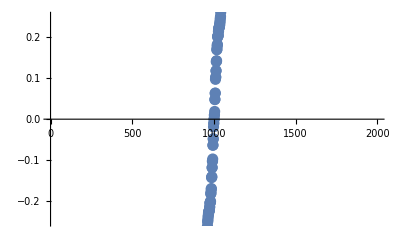

```mathematica
ListPlot[e,PlotRange->{-Δ,Δ},PlotStyle->PointSize[0.02]]
```

0.0108123

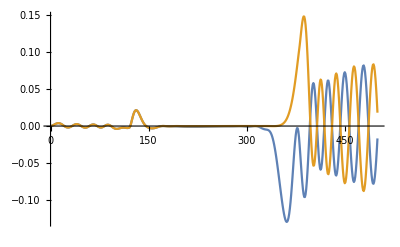

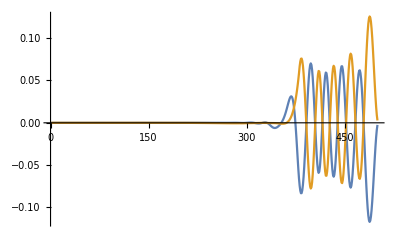

```mathematica
n=2Nx+3;
e[[n]]
ψeu=Table[ψ[[n,i]]+ψ[[n-1,i]],{i,1,2Nx,2}];
ψed=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
ListPlot[{ψeu+ψhu,ψeu-ψhu},Joined->True,PlotRange->All]
ListPlot[{ψed+ψhd,ψed-ψhd},Joined->True,PlotRange->All]
```

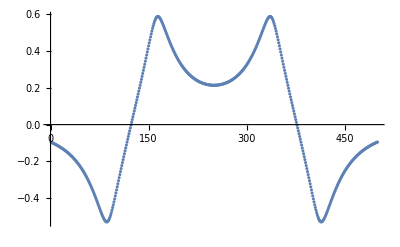

```mathematica
ListPlot[g*MagΔ]
```

```mathematica
Δ
```

0.25